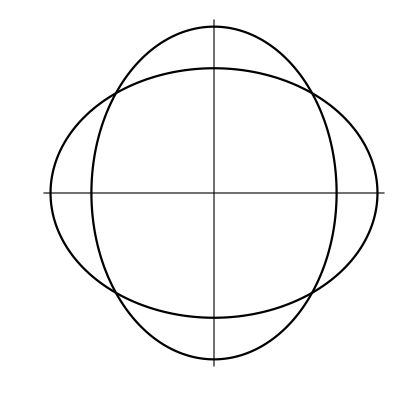

```mathematica
ParametricPlot[{{Sqrt[16]*Cos[x],Sqrt[9]*Sin[x]},{Sqrt[9]*Cos[x],Sqrt[16]*Sin[x]}},{x,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,AspectRatio->1,PlotStyle->Black]
```

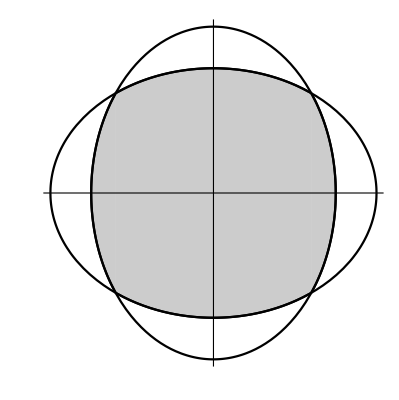

```mathematica
E0=Plot[{Sqrt[9*(1-x^2/16)],-Sqrt[9*(1-x^2/16)]},{x,-4,4},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E1=Plot[{Sqrt[9*(1-x^2/16)]},{x,-12/5,12/5},AxesStyle->Arrowheads[0.04],Filling->0,Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E2=Plot[{-Sqrt[9*(1-x^2/16)]},{x,-12/5,12/5},AxesStyle->Arrowheads[0.04],Filling->0,Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E3=Plot[{Sqrt[16*(1-x^2/9)],-Sqrt[16*(1-x^2/9)]},{x,-3,3},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E4=Plot[{Sqrt[16*(1-x^2/9)]},{x,-3,-12/5},AxesStyle->Arrowheads[0.04],Filling->0,Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E5=Plot[{-Sqrt[16*(1-x^2/9)]},{x,-3,-12/5},AxesStyle->Arrowheads[0.04],Filling->0,Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E6=Plot[{Sqrt[16*(1-x^2/9)]},{x,12/5,3},AxesStyle->Arrowheads[0.04],Filling->0,Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
E7=Plot[{-Sqrt[16*(1-x^2/9)]},{x,12/5,3},AxesStyle->Arrowheads[0.04],Filling->0,Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
Show[E0,E1,E2,E3,E4,E5,E6,E7,PlotRange->All]
```

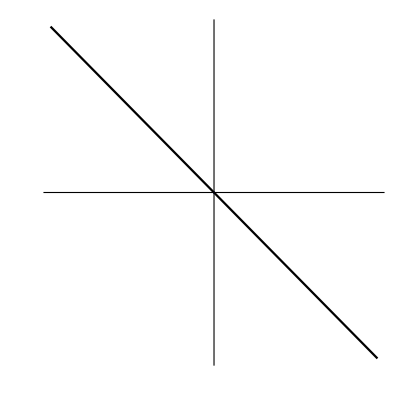

```mathematica
D1=PolarPlot[3*Cos[t]*Sin[t]/(Cos[t]^3+Sin[t]^3),{t,-Pi/4+0.0001,3*Pi/4-0.0001},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black,AspectRatio->Automatic,AxesOrigin->{0,0}];
D2=Plot[-x-1,{x,-10,10},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Blue,AspectRatio->Automatic,AxesOrigin->{0,0}];
Show[D1,D2]
```

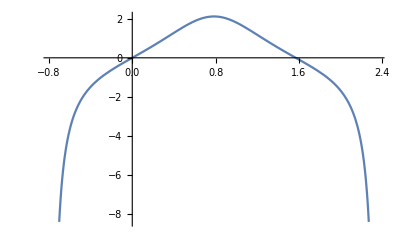

```mathematica
Plot[3*Cos[t]*Sin[t]/(Cos[t]^3+Sin[t]^3),{t,-Pi/4,3*Pi/4},AxesOrigin->{0,0}]
```

```mathematica
FindMinimum[{3*Cos[t]*Sin[t]/(Cos[t]^3+Sin[t]^3),t<3},{t,-1}]
```

{-2.12132,{t→-2.35619}}

(3 Cos[t] Sin[t])/(Cos[t]^3+Sin[t]^3)

-(3 Cos[t] Sin[t] (-3 Cos[t]^2 Sin[t]+3 Cos[t] Sin[t]^2))/((Cos[t]^3+Sin[t]^3)^2)+(3 Cos[t]^2)/(Cos[t]^3+Sin[t]^3)-(3 Sin[t]^2)/(Cos[t]^3+Sin[t]^3)

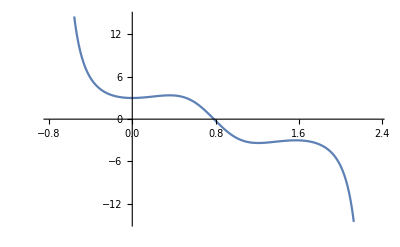

```mathematica
R[t_]=3*Cos[t]*Sin[t]/(Cos[t]^3+Sin[t]^3)
R'[t]
Plot[R'[t],{t,-Pi/4, 3*Pi/4}]
```

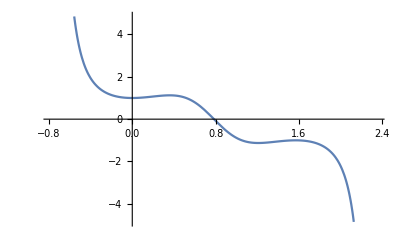

```mathematica
Plot[((Sin[2x]+1)^2 + 3 )*(Cos[x]-Sin[x])/4/(Cos[x]^3+Sin[x]^3)^2, {x, -Pi/4, 3*Pi/4},AxesOrigin->{0,0}]
```

```mathematica
FindMinimum[R'[x],{x,1.0}]
```

{-3.37781,{x→1.21124}}

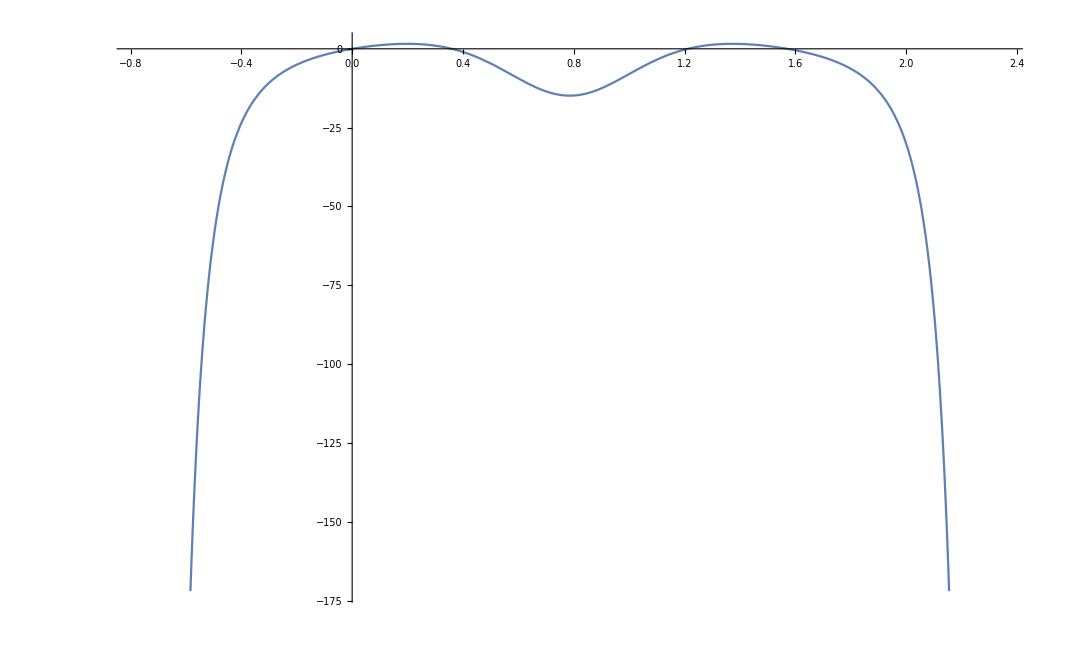

```mathematica
r[x_]=3*(Cos[x]-Sin[x])*((Sin[2x]+1)^2 + 3)/4/(Cos[x]^3+Sin[x]^3)^2;
Plot[{R''[t]},{t,-Pi/4,3*Pi/4},AxesOrigin->{0,0}]
```

WolframAlphaQueryResults

∫_0^π (sin^2(t))/((1+sin(t)) (2-sin(t))^2)ⅆt==2/3≈0.66667

```mathematica
0.6666666666666666667`5.*9/4
```

1.5

```mathematica
Integrate[R[x]^2,{x,0,Pi/2}]
```

3

```mathematica
Integrate[9*Sin[2*x]^2/4/(Cos[x]^3+Sin[x]^3)^2,{x,0,Pi/2}]
```

3